## Linear Splines

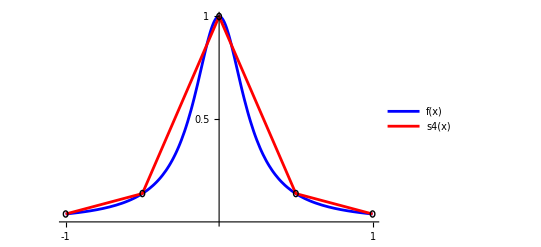

```mathematica
f[x_]=1/(1+25 x^2);
commonopts = Sequence[PlotStyle->{Directive[Blue],Directive[Red]},PlotLegends->"Expressions",PlotRange->{0,1},Ticks->{{-1,1},{-0.5,0.5,1}},ImageSize->400,PlotRangePadding->.2];
l4=Table[{x,f[x]},{x,-1,1,0.5}];
s4=Interpolation[l4,Method->"Spline",InterpolationOrder->1];Plot[{f[x],s4[x]},{x,-1,1},Evaluate[commonopts],Epilog->{Circle[#,0.015]&/@l4, Purple}]
```

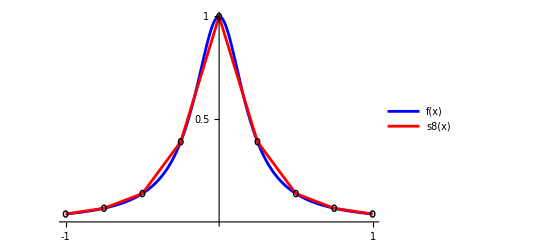

```mathematica
l8=Table[{x,f[x]},{x,-1,1,2/8}];
s8=Interpolation[l8,Method->"Spline",InterpolationOrder->1];Plot[{f[x],s8[x]},{x,-1,1},Evaluate[commonopts],Epilog->{Circle[#,0.015]&/@l8, Purple}]
```

## Cubic Splines

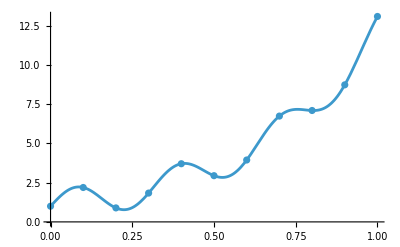

```mathematica
f[x_]=Sin[20x]+E^(5x/2);
nodelist=Table[{x,f[x]},{x,0,1,0.1}];
Show[Plot[f[x],{x,0,1}],ListPlot[nodelist]]
cs1=ResourceFunction["CubicSplineInterpolation"][nodelist,"NotAKnot"];
cs2=ResourceFunction["CubicSplineInterpolation"][nodelist,"Natural"];
cs3=ResourceFunction["CubicSplineInterpolation"][nodelist,{{"Clamped",f'[0]},{"Clamped",f'[1]}}];
```

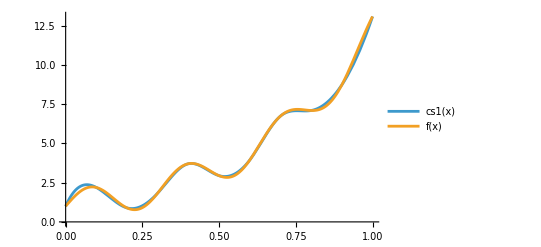

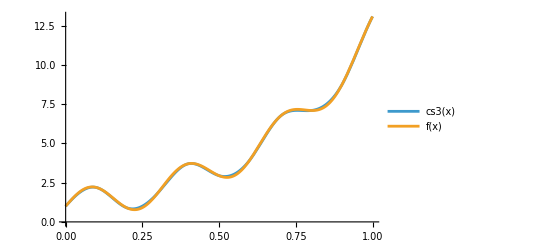

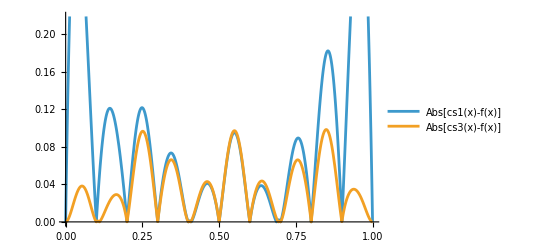

```mathematica
Plot[{cs1[x],f[x]},{x,0,1},PlotLegends->"Expressions"]
Plot[{cs3[x],f[x]},{x,0,1},PlotLegends->"Expressions"]
Plot[{Abs[cs1[x]-f[x]],Abs[cs3[x]-f[x]]},{x,0,1},PlotLegends->"Expressions"]
```

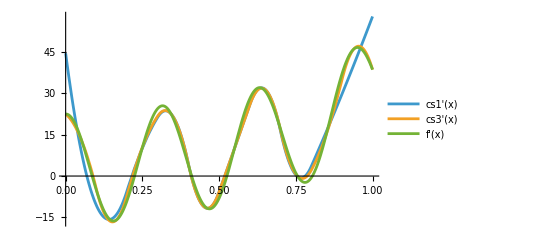

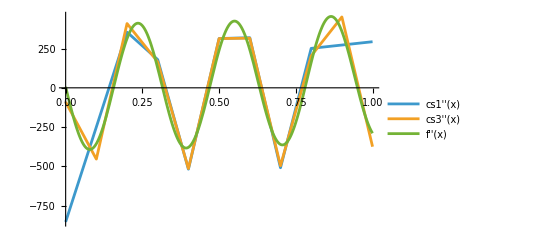

```mathematica
Plot[{cs1'[x],cs3'[x],f'[x]},{x,0,1},PlotLegends->"Expressions"]
Plot[{cs1''[x],cs3''[x],f''[x]},{x,0,1},PlotLegends->"Expressions"]
```